## t vs C Plot

The txt file to import  “coeficientes fourier for Fig 3b.nb”.
The txt file and the notebook can be found in the same folder.

### Data Import: (*change it to the local directory where the cT7.txt file is*)

```mathematica
directorio="(*your directory here*)\\";
```

#### We import the data:

```mathematica
cT7(*n,time, fourier coefficients from 11 to 20*)=Import[StringJoin[directorio,"cT7.txt"],"TSV"];

cT7=ToExpression[cT7];
```

```mathematica
mxx(*fourier coefficient value over time*)=Transpose[cT7⟦1⟧];
```

```mathematica
mx7(*index max fourier coefficient value*)=Table[Position[cT7⟦i,t⟧,Max[Abs[cT7⟦i,t⟧]]]⟦1,1⟧,{i,1,Dimensions[cT7]⟦1⟧},{t,1,Dimensions[cT7]⟦2⟧}]
```

{{9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}}

Here we can observe that the index 9, 2, 4 and 3  are the important ones; we will use this information for the variable “list”.

```mathematica
gra7(*max fourier coefficient value*)=Table[cT7⟦i,t,mx7⟦i,t⟧⟧,{i,1,Length[cT7]},{t,1,Dimensions[cT7]⟦2⟧}];
```

### Time step (to adjust the scale):

Time Step

```mathematica
tn7=Table[i,{i,0,138.785076,0.41673032696730333}];
```

Natural time

```mathematica
list=Table[Transpose[{tn7,Join[gra7,mxx⟦9;;9⟧(*index 9(the 19 fourier coefficient)*),mxx⟦2;;4⟧(*index 2 to 4 (the 12 to 14 fourier coefficient)*)]⟦i⟧}],{i,1,Length[Join[gra7,mxx⟦9;;9⟧,mxx⟦2;;4⟧]]}];
```

### Plots:

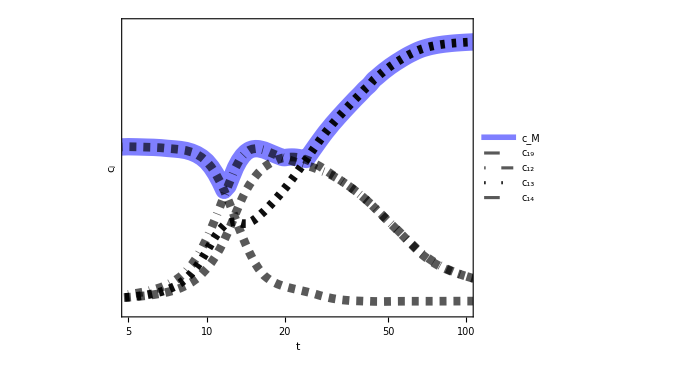

```mathematica
C7s=ListLogLinearPlot[list,PlotRange->{{5,100},{-0.02,.58}},Joined->True,AspectRatio->0.75, Frame->True, FrameTicks->{{None,{0,.2,.4,.6}},{None,{5,10,50,100}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["t",38,Italic, Black]],Text[Style["c_j",38,Italic, Black]]},PlotStyle->{{Opacity[0.5,Blue],Thickness[0.025]},{Opacity[0.65,Black],Thickness[0.0125],Dashed},{Opacity[0.65,Black],Thickness[0.0125],DotDashed},{Opacity[0.95,Black],Thickness[0.0125],Dashing[{0.0065,Small}]},{Opacity[0.65,Black],Thickness[0.0125],Dashed}},PlotLegends->{ "c_M","c_19","c_12","c_13","c_14"}]
```

```mathematica
Export["figura3b.png",C7s,ImageResolution->250]
```

figura3b.png